```mathematica
Quit[]
```

# MeV-DM: Scalar Mediator model

Load `HazmaTools`.Note that this will load `FeynCalc` and the patched `FeynArts`

```mathematica
Import[NotebookDirectory[]<>"../HazmaTools/HazmaTools.m"]
$HazmaModel="scalar";
```

FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

args::shdw: Symbol args appears in multiple contexts {FeynArts`,Global`}; definitions in context FeynArts` may shadow or be shadowed by other definitions.

FeynArts 3.1 patched for use with FeynCalc, for documentation use the manual or visit www.feynarts.de.

MeV-DM - Scalar Mediator: version 1.0

by Adam Coogan and Logan A. Morrison

## Amplitudes

```mathematica
(* x + xbar-> l + lbar *)
amplitudeLL=HazmaCreateAmplitude[{statex,statexbar},{statel,statelbar},IncomingMomenta->{px,pxbar},OutgoingMomenta->{pl,plbar}];
(* x + xbar-> gamma + gamma *)
amplitudeGG=HazmaCreateAmplitude[{statex,statexbar},{stateγ,stateγ}];
(* x + xbar-> pi0 + pi0 *)
amplitudeπ0π0=HazmaCreateAmplitude[{statex,statexbar},{stateπ0,stateπ0}];
(* x + xbar-> pi + pi *)
amplitudeπpπm=HazmaCreateAmplitude[{statex,statexbar},{stateπp,stateπm}];
(* x + xbar-> S + S *)
amplitudeSS=HazmaCreateAmplitude[{statex,statexbar},{states,states}];
```

## Squared Amplitudes

```mathematica
(* x + xbar-> l + lbar *)
msqrdLL=HazmaCreateAmplitudeSquared[{statex,statexbar},{statel,statelbar},IncomingMomenta->{px,pxbar},OutgoingMomenta->{pl,plbar}];
(* x + xbar-> gamma + gamma *)
msqrdGG=HazmaCreateAmplitudeSquared[{statex,statexbar},{stateγ,stateγ}];
(* x + xbar-> pi0 + pi0 *)
msqrdπ0π0=HazmaCreateAmplitudeSquared[{statex,statexbar},{stateπ0,stateπ0}];
(* x + xbar-> pi + pi *)
msqrdπpπm=HazmaCreateAmplitudeSquared[{statex,statexbar},{stateπp,stateπm}];
(* x + xbar-> S + S *)
msqrdSS=HazmaCreateAmplitudeSquared[{statex,statexbar},{states,states}];
```

## Cross Sections

To Compute cross sections for 2->2 interactions, use: `HazmaComputeCrossSection22[inStates,outStates, ECM]`, where `inStates` and `outStates` are arrays of particles states and `ECM` is the variable for the center of mass energy.

```mathematica
(* x + xbar-> l + lbar *)
crossSectionLL=HazmaComputeCrossSection22[{statex,statexbar},{statel,statelbar},Q];
(* x + xbar-> gamma + gamma *)
crossSectionGG=HazmaComputeCrossSection22[{statex,statexbar},{stateγ,stateγ},Q];
(* x + xbar-> pi0 + pi0 *)
crossSectionπ0π0=HazmaComputeCrossSection22[{statex,statexbar},{stateπ0,stateπ0},Q];
(* x + xbar-> pi + pi *)
crossSectionπpπm=HazmaComputeCrossSection22[{statex,statexbar},{stateπp,stateπm},Q];
(* x + xbar-> S + S *)
crossSectionSS=HazmaComputeCrossSection22[{statex,statexbar},{states,states},Q];
```

## FSR Spectra

NOTE: You do not need to specify the photon in the `outStates`.

```mathematica
(* x + xbar -> l + lbar + gamma *)
dndeLL=HazmaComputeDNDE[{statex,statexbar},{statel,statelbar},Q];
```

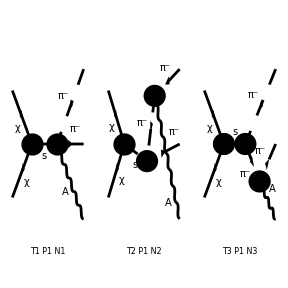

```mathematica
(* x + xbar -> pi + pi + gamma *)
dndeππ=HazmaComputeDNDE[{statex,statexbar},{stateπp,stateπm},Q,Paint->True];
```

```mathematica
$HazmaModel="vector"
```

vector

```mathematica
ScalarProduct[px,px]=mx^2;
ScalarProduct[pxbar,pxbar]=mx^2;
```

```mathematica
amp=HazmaCreateAmplitude[{statex,statexbar},{statev},IncomingMomenta->{px,pxbar},OutgoingMomenta->{P},LorentzIndexNames->{μ}];
amp=ReplaceAll[amp,{Pair[LorentzIndex[a__],Momentum[Polarization[p__,-I]]]:>1}];
ampConj=ReplaceAll[ComplexConjugate[amp],μ->ν];
```

```mathematica
msqrd=DoPolarizationSums[ReplaceAll[FermionSpinSum[amp*ampConj],DiracTrace->TR],P]
```

-12 gvxx^2 (mx^2 (ḡ)^μν+(ḡ)^μν (OverBar[px]·OverBar[pxbar])-OverBar[px]^ν OverBar[pxbar]^μ-OverBar[px]^μ OverBar[pxbar]^ν)

```mathematica
Contract[(FourVector[px,μ]+FourVector[pxbar,μ])msqrd]//Simplify
```

-12 gvxx^2 ((mx^2-OverBar[px]^2) OverBar[pxbar]^ν+(mx^2-OverBar[pxbar]^2) OverBar[px]^ν)

```mathematica
DoPolarizationSums[ReplaceAll[FermionSpinSum[ComplexConjugate[HazmaCreateAmplitude[{statex,statexbar},{statev}]]HazmaCreateAmplitude[{statex,statexbar},{statev}]],DiracTrace->TR],
```

-8 gvxx^2 ((ε̄)^*)^μ(OutMom1) (ε̄)^μ(OutMom1) (OverBar[InMom1]·OverBar[InMom2]+2 mx^2)

```mathematica
SP[k,k]=0;
```

```mathematica
amp=HazmaCreateAmplitude[{statev},{statel,statelbar,stateγ},IncomingMomenta->{P},OutgoingMomenta->{pl,plbar,k},LorentzIndexNames->{μ}];
amp=ReplaceAll[amp,{DiracGamma[Momentum[Polarization[P,I]]]:>GA[μ]}];
ampConj=ReplaceAll[ComplexConjugate[amp],μ->ν];
```

```mathematica
amp
```

```mathematica
Simplify[Contract[MT[μ,ν]DoPolarizationSums[ReplaceAll[FermionSpinSum[ampConj*amp],DiracTrace->TR],k,0]]]
```

PolarizationSum::notmassless: Warning! You are inserting a polarization sum for massless vector bosons, but the momentum of the external boson k is not on-shell. Please put it on-shell via ScalarProduct[k,k]=0

General::stop: Further output of PolarizationSum::notmassless will be suppressed during this calculation.

(16 gvll^2 qe^2 ((6 ml^2-2 (OverBar[pl]·OverBar[plbar])) (k̄)^6-2 (6 ml^4-5 OverBar[pl]^2 ml^2+2 (OverBar[pl]·OverBar[plbar]) ml^2-5 OverBar[plbar]^2 ml^2+2 (OverBar[pl]·OverBar[plbar])^2-2 (k̄·OverBar[plbar]) (3 ml^2+OverBar[pl]^2-2 (OverBar[pl]·OverBar[plbar]))-2 (k̄·OverBar[pl]) (3 ml^2-k̄·OverBar[plbar]-2 (OverBar[pl]·OverBar[plbar])+OverBar[plbar]^2)) (k̄)^4+(6 ml^6-14 OverBar[pl]^2 ml^4+14 (OverBar[pl]·OverBar[plbar]) ml^4-14 OverBar[plbar]^2 ml^4+4 OverBar[pl]^4 ml^2+8 (OverBar[pl]·OverBar[plbar])^2 ml^2+4 OverBar[plbar]^4 ml^2-10 OverBar[pl]^2 (OverBar[pl]·OverBar[plbar]) ml^2+14 OverBar[pl]^2 OverBar[plbar]^2 ml^2-10 (OverBar[pl]·OverBar[plbar]) OverBar[plbar]^2 ml^2-4 OverBar[pl]^2 (OverBar[pl]·OverBar[plbar])^2+(OverBar[pl]·OverBar[plbar]) OverBar[plbar]^4+4 (k̄·OverBar[plbar])^2 (2 ml^2+3 OverBar[pl]^2-OverBar[pl]·OverBar[plbar])+OverBar[pl]^4 (OverBar[pl]·OverBar[plbar])-4 (OverBar[pl]·OverBar[plbar])^2 OverBar[plbar]^2+4 OverBar[pl]^2 (OverBar[pl]·OverBar[plbar]) OverBar[plbar]^2+4 (k̄·OverBar[pl])^2 (2 ml^2-2 (k̄·OverBar[plbar])-OverBar[pl]·OverBar[plbar]+3 OverBar[plbar]^2)-2 (k̄·OverBar[plbar]) (6 ml^4+2 (OverBar[pl]·OverBar[plbar]) ml^2-6 OverBar[plbar]^2 ml^2-OverBar[pl]^4+4 (OverBar[pl]·OverBar[plbar])^2+OverBar[pl]^2 (-4 ml^2+2 (OverBar[pl]·OverBar[plbar])-3 OverBar[plbar]^2))-2 (k̄·OverBar[pl]) (6 ml^4+2 (OverBar[pl]·OverBar[plbar]) ml^2-4 OverBar[plbar]^2 ml^2+4 (k̄·OverBar[plbar])^2+4 (OverBar[pl]·OverBar[plbar])^2-OverBar[plbar]^4-8 (k̄·OverBar[plbar]) (ml^2-2 (OverBar[pl]·OverBar[plbar]))+2 (OverBar[pl]·OverBar[plbar]) OverBar[plbar]^2-3 OverBar[pl]^2 (2 ml^2+OverBar[plbar]^2))) (k̄)^2+2 (-4 (k̄·OverBar[plbar]-OverBar[plbar]^2) (k̄·OverBar[pl])^3+2 (2 ml^4+2 (OverBar[pl]·OverBar[plbar]) ml^2-OverBar[plbar]^2 ml^2+OverBar[plbar]^4+2 OverBar[pl]^2 OverBar[plbar]^2+2 (k̄·OverBar[plbar]) (ml^2-OverBar[pl]^2-2 (OverBar[pl]·OverBar[plbar])+OverBar[plbar]^2)) (k̄·OverBar[pl])^2+(6 (OverBar[pl]·OverBar[plbar]) ml^4-8 OverBar[plbar]^2 ml^4+4 (OverBar[pl]·OverBar[plbar])^2 ml^2+OverBar[plbar]^4 ml^2-10 (OverBar[pl]·OverBar[plbar]) OverBar[plbar]^2 ml^2-4 (k̄·OverBar[plbar])^3+4 (k̄·OverBar[plbar])^2 (ml^2+OverBar[pl]^2-2 (OverBar[pl]·OverBar[plbar])-OverBar[plbar]^2)+OverBar[pl]^4 OverBar[plbar]^2-4 (OverBar[pl]·OverBar[plbar])^2 OverBar[plbar]^2+OverBar[pl]^2 (ml^2+OverBar[plbar]^2) (2 ml^2+2 (OverBar[pl]·OverBar[plbar])+OverBar[plbar]^2)-(k̄·OverBar[plbar]) (10 ml^4-4 OverBar[plbar]^2 ml^2+OverBar[pl]^4+8 (OverBar[pl]·OverBar[plbar])^2+OverBar[plbar]^4+4 (OverBar[pl]·OverBar[plbar]) (2 ml^2+OverBar[plbar]^2)-4 OverBar[pl]^2 (ml^2-OverBar[pl]·OverBar[plbar]+OverBar[plbar]^2))) (k̄·OverBar[pl])+4 (k̄·OverBar[plbar])^3 OverBar[pl]^2+2 (k̄·OverBar[plbar])^2 (2 (ml^2+OverBar[pl]·OverBar[plbar]) ml^2+OverBar[pl]^4-OverBar[pl]^2 (ml^2-2 OverBar[plbar]^2))+(2 ml^2+OverBar[pl]·OverBar[plbar]) (OverBar[plbar]^2 ml^4+OverBar[pl]^4 OverBar[plbar]^2-2 (OverBar[pl]·OverBar[plbar]) (ml^4-ml^2 OverBar[plbar]^2)+OverBar[pl]^2 (ml^4-4 OverBar[plbar]^2 ml^2+OverBar[plbar]^4+2 (OverBar[pl]·OverBar[plbar]) (ml^2-OverBar[plbar]^2)))+(k̄·OverBar[plbar]) (2 (OverBar[plbar]^2 ml^2+2 (OverBar[pl]·OverBar[plbar])^2+(OverBar[pl]·OverBar[plbar]) (3 ml^2+OverBar[plbar]^2)) ml^2+OverBar[pl]^4 (ml^2+OverBar[plbar]^2)+OverBar[pl]^2 (-8 ml^4+3 OverBar[plbar]^2 ml^2-4 (OverBar[pl]·OverBar[plbar])^2+OverBar[plbar]^4+2 (OverBar[pl]·OverBar[plbar]) (OverBar[plbar]^2-5 ml^2))))))/((-ml^2+(k̄)^2+2 (k̄·OverBar[pl])+OverBar[pl]^2)^2 (-ml^2+(k̄)^2+2 (k̄·OverBar[plbar])+OverBar[plbar]^2)^2)

```mathematica
Uncontract[amp,P]
```

-(gvll qe (ε̄)^($AL$19744(1))(P) (φ(OverBar[pl],ml)).(γ̄·(ε̄)^*(l)).(γ̄·l̄).(γ̄)^($AL$19744(1)).(φ(-OverBar[plbar],ml)))/(2 (l̄·OverBar[pl])+(l̄)^2+OverBar[pl]^2-ml^2)-(2 gvll qe (ε̄)^($AL$19745(1))(P) (OverBar[pl]·(ε̄)^*(l)) (φ(OverBar[pl],ml)).(γ̄)^($AL$19745(1)).(φ(-OverBar[plbar],ml)))/(2 (l̄·OverBar[pl])+(l̄)^2+OverBar[pl]^2-ml^2)+(gvll qe (ε̄)^($AL$19746(1))(P) (φ(OverBar[pl],ml)).(γ̄)^($AL$19746(1)).(γ̄·l̄).(γ̄·(ε̄)^*(l)).(φ(-OverBar[plbar],ml)))/(2 (l̄·OverBar[plbar])+(l̄)^2+OverBar[plbar]^2-ml^2)+(2 gvll qe (ε̄)^($AL$19747(1))(P) (OverBar[plbar]·(ε̄)^*(l)) (φ(OverBar[pl],ml)).(γ̄)^($AL$19747(1)).(φ(-OverBar[plbar],ml)))/(2 (l̄·OverBar[plbar])+(l̄)^2+OverBar[plbar]^2-ml^2)